Dirac neutrinos in the singlet-doublet Dirac DM

```mathematica
Quit;
```

```mathematica
ClearAll["Global`*"];
$FeynArtsPath=SetDirectory["~/Work/FeynArts-3.9"]
<<FeynArts`
SetDirectory[$FeynArtsPath<>""]
$FormCalcPath=SetDirectory["~/Work/FormCalc-8.3"]
<<FormCalc`
SetDirectory[$FormCalcPath<>""]
```

/home/anferivera/Work/FeynArts-3.9

FeynArts 3.9 (8 Jul 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

/home/anferivera/Work/FeynArts-3.9

/home/anferivera/Work/FormCalc-8.3

FormCalc 8.3

by Thomas Hahn

last revised 14 Nov 13

/home/anferivera/Work/FormCalc-8.3

For Simbolic linking uncoment(coment) the next(last) lines

```mathematica
(*ClearAll["Global`*"];
<<FeynArts`
<<FormCalc`*)
```

FeynArts 3.9

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 11 Jul 14

FormCalc 8.3

by Thomas Hahn

last revised 14 Nov 13

Process:    S^0 ν_R ⟶ ϕ^0ν_L

Only one family

```mathematica
T2DM2S=CreateTopologies[1,1->1,ExcludeTopologies->{(*SelfEnergies,Tadpoles,*)Internal}];
```

> Top. 1: 1 diagram

> Top. 2: 1 diagram

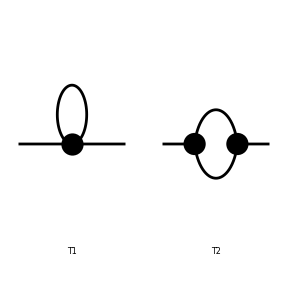

FeynArtsGraphics[1→1][([T1] | [T2] | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[T2DM2S]
```

loading generic model file /home/anferivera/Work/FeynArts-3.9/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/anferivera/Work/FeynArts-3.9/Models/SDdiracDMvsEWSB.mod

> 52 particles (incl. antiparticles) in 19 classes

> $CounterTerms are ON

> 114 vertices

classes model {SDdiracDMvsEWSB} initialized

Excluding 0 Generic, 3 Classes, and 9 Particles fields

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 4 Particles insertions

Restoring 0 Generic, 3 Classes, and 9 Particles fields

in total: 4 Particles insertions

> Top. 1: 4 diagrams

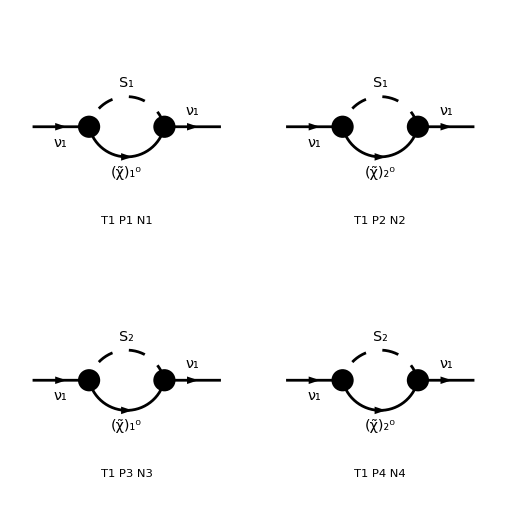

FeynArtsGraphics[{ComposedChar[\nu,1]}→{ComposedChar[\nu,1]}][([T1 P1 N1] | [T1 P2 N2]
[T1 P3 N3] | [T1 P4 N4])]

```mathematica
n11=InsertFields[T2DM2S,{F[1,{1}]}->{F[1,{1}]},InsertionLevel->{Particles},Model->"SDdiracDMvsEWSB",GenericModel->"Lorentz",ExcludeParticles->{F[2,{1}],F[2,{2}],F[2,{3}],V[2],V[3]}];
Paint[n11,ColumnsXRows->2]
```

Amplitude in process..

```mathematica
CreateFeynAmp[n11]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

in total: 4 Particles amplitudes

FeynAmpList[Process→{{F[1,{1}],p1,MassFv[1],{}}}→{{F[1,{1}],k1,MassFv[1],{}}},Model→{SDdiracDMvsEWSB},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{-F[2,{1}],F[2,{1}],-F[2,{2}],F[2,{2}],-F[2,{3}],F[2,{3}],V[2],-V[3],V[3]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[q1],1/(16 π^4)ⅈ ū[k1,MassFv[1]].(-ⅈ XV[1,1]^* om_- (IndexSum[UVR[1,j1]^* YRB1[j1],{j1,3}] VSs[1,1]+IndexSum[UVR[1,j1]^* YRB2[j1],{j1,3}] VSs[1,2])-ⅈ om_+ (IndexSum[UV[1,j1] YRA1[j1],{j1,3}] VSs[1,1]+IndexSum[UV[1,j1] YRA2[j1],{j1,3}] VSs[1,2]) XU[1,2]).(gs[q1]+MassFxv[1]).(-ⅈ XU[1,2]^* om_- (IndexSum[UV[1,j1]^* YRA1[j1],{j1,3}] VSs[1,1]+IndexSum[UV[1,j1]^* YRA2[j1],{j1,3}] VSs[1,2])-ⅈ om_+ (IndexSum[UVR[1,j1] YRB1[j1],{j1,3}] VSs[1,1]+IndexSum[UVR[1,j1] YRB2[j1],{j1,3}] VSs[1,2]) XV[1,1]).u[p1,MassFv[1]] FeynAmpDenominator[1/((q1)^2-MassFxv[1]^2),1/((q1-k1)^2-MassSs[1]^2)]],FeynAmp[GraphID[Topology==1,Generic==1,Particles==2,Number==2],Integral[q1],1/(16 π^4)ⅈ ū[k1,MassFv[1]].(-ⅈ XV[2,1]^* om_- (IndexSum[UVR[1,j1]^* YRB1[j1],{j1,3}] VSs[1,1]+IndexSum[UVR[1,j1]^* YRB2[j1],{j1,3}] VSs[1,2])-ⅈ om_+ (IndexSum[UV[1,j1] YRA1[j1],{j1,3}] VSs[1,1]+IndexSum[UV[1,j1] YRA2[j1],{j1,3}] VSs[1,2]) XU[2,2]).(gs[q1]+MassFxv[2]).(-ⅈ XU[2,2]^* om_- (IndexSum[UV[1,j1]^* YRA1[j1],{j1,3}] VSs[1,1]+IndexSum[UV[1,j1]^* YRA2[j1],{j1,3}] VSs[1,2])-ⅈ om_+ (IndexSum[UVR[1,j1] YRB1[j1],{j1,3}] VSs[1,1]+IndexSum[UVR[1,j1] YRB2[j1],{j1,3}] VSs[1,2]) XV[2,1]).u[p1,MassFv[1]] FeynAmpDenominator[1/((q1)^2-MassFxv[2]^2),1/((q1-k1)^2-MassSs[1]^2)]],FeynAmp[GraphID[Topology==1,Generic==1,Particles==3,Number==3],Integral[q1],1/(16 π^4)ⅈ ū[k1,MassFv[1]].(-ⅈ XV[1,1]^* om_- (IndexSum[UVR[1,j1]^* YRB1[j1],{j1,3}] VSs[2,1]+IndexSum[UVR[1,j1]^* YRB2[j1],{j1,3}] VSs[2,2])-ⅈ om_+ (IndexSum[UV[1,j1] YRA1[j1],{j1,3}] VSs[2,1]+IndexSum[UV[1,j1] YRA2[j1],{j1,3}] VSs[2,2]) XU[1,2]).(gs[q1]+MassFxv[1]).(-ⅈ XU[1,2]^* om_- (IndexSum[UV[1,j1]^* YRA1[j1],{j1,3}] VSs[2,1]+IndexSum[UV[1,j1]^* YRA2[j1],{j1,3}] VSs[2,2])-ⅈ om_+ (IndexSum[UVR[1,j1] YRB1[j1],{j1,3}] VSs[2,1]+IndexSum[UVR[1,j1] YRB2[j1],{j1,3}] VSs[2,2]) XV[1,1]).u[p1,MassFv[1]] FeynAmpDenominator[1/((q1)^2-MassFxv[1]^2),1/((q1-k1)^2-MassSs[2]^2)]],FeynAmp[GraphID[Topology==1,Generic==1,Particles==4,Number==4],Integral[q1],1/(16 π^4)ⅈ ū[k1,MassFv[1]].(-ⅈ XV[2,1]^* om_- (IndexSum[UVR[1,j1]^* YRB1[j1],{j1,3}] VSs[2,1]+IndexSum[UVR[1,j1]^* YRB2[j1],{j1,3}] VSs[2,2])-ⅈ om_+ (IndexSum[UV[1,j1] YRA1[j1],{j1,3}] VSs[2,1]+IndexSum[UV[1,j1] YRA2[j1],{j1,3}] VSs[2,2]) XU[2,2]).(gs[q1]+MassFxv[2]).(-ⅈ XU[2,2]^* om_- (IndexSum[UV[1,j1]^* YRA1[j1],{j1,3}] VSs[2,1]+IndexSum[UV[1,j1]^* YRA2[j1],{j1,3}] VSs[2,2])-ⅈ om_+ (IndexSum[UVR[1,j1] YRB1[j1],{j1,3}] VSs[2,1]+IndexSum[UVR[1,j1] YRB2[j1],{j1,3}] VSs[2,2]) XV[2,1]).u[p1,MassFv[1]] FeynAmpDenominator[1/((q1)^2-MassFxv[2]^2),1/((q1-k1)^2-MassSs[2]^2)]]]

```mathematica
resultn11=CalcFeynAmp[CreateFeynAmp[n11],FermionChains->VA,Antisymmetrize->False,Invariants->True];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

in total: 4 Particles amplitudes

preparing FORM code in /home/anferivera/Work/FormCalc-8.3/fc-amp-1.frm

running FORM...

ok

```mathematica
resultn11
```

Amp[{{F[1,{1}],k[1],MassFv[1],{}}}→{{F[1,{1}],k[2],MassFv[1],{}}}][(1/(32 π^2)((Sub20 B0i[bb1,MassFv[1]^2,MassFxv[1]^2,MassSs[1]^2]+Sub22 B0i[bb1,MassFv[1]^2,MassFxv[1]^2,MassSs[2]^2]+Sub12 B0i[bb1,MassFv[1]^2,MassFxv[2]^2,MassSs[1]^2]+Sub17 B0i[bb1,MassFv[1]^2,MassFxv[2]^2,MassSs[2]^2]) MassFv[1]+Sub6 (Sub3 B0i[bb0,MassFv[1]^2,MassFxv[1]^2,MassSs[1]^2]+Sub5 B0i[bb0,MassFv[1]^2,MassFxv[1]^2,MassSs[2]^2]) MassFxv[1]+Sub1 (Sub3 B0i[bb0,MassFv[1]^2,MassFxv[2]^2,MassSs[1]^2]+Sub5 B0i[bb0,MassFv[1]^2,MassFxv[2]^2,MassSs[2]^2]) MassFxv[2]) Mat[F1]+1/π^2(1/32 (Sub21 B0i[bb1,MassFv[1]^2,MassFxv[1]^2,MassSs[1]^2]+Sub23 B0i[bb1,MassFv[1]^2,MassFxv[1]^2,MassSs[2]^2]+Sub18 B0i[bb1,MassFv[1]^2,MassFxv[2]^2,MassSs[1]^2]+Sub19 B0i[bb1,MassFv[1]^2,MassFxv[2]^2,MassSs[2]^2]) MassFv[1]+1/32 (-Sub7 (Sub3 B0i[bb0,MassFv[1]^2,MassFxv[1]^2,MassSs[1]^2]+Sub5 B0i[bb0,MassFv[1]^2,MassFxv[1]^2,MassSs[2]^2]) MassFxv[1]-Sub4 (Sub3 B0i[bb0,MassFv[1]^2,MassFxv[2]^2,MassSs[1]^2]+Sub5 B0i[bb0,MassFv[1]^2,MassFxv[2]^2,MassSs[2]^2]) MassFxv[2])) Mat[F2]) SumOver[Ind1,3] SumOver[Ind2,3]]

Simplifications

```mathematica
Den[x_,y_]:=1/(x-y)

expr1=Simplify[ComplexExpand[ Plus@@resultn11//.Subexpr[]//.Abbr[] //.{MassFxv[1]->m1,MassFxv[2]->m2,MassFv[1]->0,MassFv[2]->0,MassSs[1]->Ms1,MassSs[2]->Ms2}//.{XU[1,1]->XU11,XU[2,2]->XU22,XU[1,2]->XU12,XU[2,1]->XU21}//.{XV[1,1]->XV11,XV[2,2]->XV22,XV[1,2]->XV12,XV[2,1]->XV21}
]]
```

-1/(16 π^2)Mat[<v1|1|v2>] SumOver[Ind1,3] SumOver[Ind2,3] UV[1,Ind1] UVR[1,Ind2] (m1 XU12 XV11 B0i[bb0,0,m1^2,Ms1^2] (VSs[1,1] YRA1[Ind1]+VSs[1,2] YRA2[Ind1]) (VSs[1,1] YRB1[Ind2]+VSs[1,2] YRB2[Ind2])+m2 XU22 XV21 B0i[bb0,0,m2^2,Ms1^2] (VSs[1,1] YRA1[Ind1]+VSs[1,2] YRA2[Ind1]) (VSs[1,1] YRB1[Ind2]+VSs[1,2] YRB2[Ind2])+(m1 XU12 XV11 B0i[bb0,0,m1^2,Ms2^2]+m2 XU22 XV21 B0i[bb0,0,m2^2,Ms2^2]) (VSs[2,1] YRA1[Ind1]+VSs[2,2] YRA2[Ind1]) (VSs[2,1] YRB1[Ind2]+VSs[2,2] YRB2[Ind2]))

```mathematica
expr2 = expr1//.{VSs[1,1]->VS11,VSs[1,2]->0,VSs[2,1]->0,VSs[2,2]->VS22}
```

-1/(16 π^2)Mat[<v1|1|v2>] SumOver[Ind1,3] SumOver[Ind2,3] UV[1,Ind1] UVR[1,Ind2] (m1 VS11^2 XU12 XV11 B0i[bb0,0,m1^2,Ms1^2] YRA1[Ind1] YRB1[Ind2]+m2 VS11^2 XU22 XV21 B0i[bb0,0,m2^2,Ms1^2] YRA1[Ind1] YRB1[Ind2]+VS22^2 (m1 XU12 XV11 B0i[bb0,0,m1^2,Ms2^2]+m2 XU22 XV21 B0i[bb0,0,m2^2,Ms2^2]) YRA2[Ind1] YRB2[Ind2])

Write the SUM:
∑_(ij=1)^3 expr3

```mathematica
expr3=FullSimplify[expr2/(SumOver[Ind1,3] SumOver[Ind2,3])]
```

-1/(16 π^2)Mat[<v1|1|v2>] UV[1,Ind1] UVR[1,Ind2] (VS11^2 (m1 XU12 XV11 B0i[bb0,0,m1^2,Ms1^2]+m2 XU22 XV21 B0i[bb0,0,m2^2,Ms1^2]) YRA1[Ind1] YRB1[Ind2]+VS22^2 (m1 XU12 XV11 B0i[bb0,0,m1^2,Ms2^2]+m2 XU22 XV21 B0i[bb0,0,m2^2,Ms2^2]) YRA2[Ind1] YRB2[Ind2])

Eigenenergy:
∑_αβ=∑_(ij=1)^3 M_αβij<v1|v2>

```mathematica
M11ij=Simplify[(expr3//.{UV[1,Ind1]->UV1i,UVR[1,Ind2]->UVR1j,YRA1[Ind1]->a1i,YRB1[Ind2]->b1j,YRA2[Ind1]->a2i,YRB2[Ind2]->b2j})]/(Mat[DiracChain[Spinor[k[1],0,-1],1,Spinor[k[2],0,-1]]])
```

-(UV1i UVR1j (a1i b1j VS11^2 (m1 XU12 XV11 B0i[bb0,0,m1^2,Ms1^2]+m2 XU22 XV21 B0i[bb0,0,m2^2,Ms1^2])+a2i b2j VS22^2 (m1 XU12 XV11 B0i[bb0,0,m1^2,Ms2^2]+m2 XU22 XV21 B0i[bb0,0,m2^2,Ms2^2])))/(16 π^2)

#### Compute the Passarino - Veltman funtions

## X - Package

```mathematica
<<X`
```

\!\(\*TemplateBox[List["\"Package-X v2.1.1 already initialized\\nFor more information, see the \"", TagBox[ButtonBox[PaneSelectorBox[List[Rule[False, "\"guide\""], Rule[True, StyleBox["\"guide\"", List["HyperlinkActive"]]]], Dynamic[CurrentValue["MouseOver"]], Rule[BaseStyle, List["Hyperlink"]], Rule[FrameMargins, 0], Rule[ImageSize, Automatic]], Rule[BaseStyle, "Link"], Rule[ButtonData, "paclet:X/guide/PackageX"], Rule[ButtonNote, "paclet:X/guide/PackageX"]], Function[Annotation[Slot[1], "paclet:X/guide/PackageX", "Hyperlink"]]]], "RowDefault"]\)

```mathematica
LooptoolstoXpackage2={
B0i[bb0,p1_,m1_,m2_]->PVB[0,0,p1,Sqrt[m1],Sqrt[m2]],B0i[bb1,p1_,m1_,m2_]->PVB[0,1,p1,Sqrt[m1],Sqrt[m2]],
C0i[cc0,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[0,0,0,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc1,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[0,1,0,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc2,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[0,0,1,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc00,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[1,0,0,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc11,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[0,2,0,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc12,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[0,1,1,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc22,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[0,0,2,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc001,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[1,1,0,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc002,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[1,0,1,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc111,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[0,3,0,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc112,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[0,2,1,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc122,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[0,1,2,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc222,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[0,0,3,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc0000,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[2,0,0,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc0011,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[1,2,0,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc0012,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[1,1,1,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc0022,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[1,0,2,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc1111,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[0,4,0,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc1112,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[0,3,1,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc1122,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[0,2,2,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc1222,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[0,1,3,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]],
C0i[cc2222,p1_,p2_,p12_,m1_,m2_,m3_]->PVC[0,0,4,p1,p2,p12,Sqrt[m1],Sqrt[m2],Sqrt[m3]]
};
```

```mathematica
expr4=Simplify[LoopRefine[M11ij/.LooptoolstoXpackage2]]
```

1/(16 π^2)UV1i UVR1j (-(a1i b1j VS11^2+a2i b2j VS22^2) (m1 XU12 XV11+m2 XU22 XV21)-(a1i b1j VS11^2 (-m1 Ms1^2 XU12 XV11+m1^2 m2 XU22 XV21-m2 Ms1^2 XU22 XV21) Log[m1^2/Ms1^2])/(m1^2-Ms1^2)+(a1i b1j m2^3 VS11^2 XU22 XV21 Log[m2^2/Ms1^2])/(m2^2-Ms1^2)-(a2i b2j VS22^2 (-m1 Ms2^2 XU12 XV11+m1^2 m2 XU22 XV21-m2 Ms2^2 XU22 XV21) Log[m1^2/Ms2^2])/(m1^2-Ms2^2)+(a2i b2j m2^3 VS22^2 XU22 XV21 Log[m2^2/Ms2^2])/(m2^2-Ms2^2)-(a1i b1j VS11^2+a2i b2j VS22^2) (m1 XU12 XV11+m2 XU22 XV21) (1/ϵ+Log[µ^2/m1^2]))

WANING!!! Probe that : (m1 XU12 XV11 + m2 XU22 XV21) -> 0

```mathematica
Simplify[expr4//.{ m1 XU12 XV11->-m2 XU22 XV21,VS11->1,VS22->1}]
```

(m2 UV1i UVR1j XU22 XV21 (-(a1i b1j m1^2 Log[m1^2/Ms1^2])/(m1^2-Ms1^2)+(a1i b1j m2^2 Log[m2^2/Ms1^2])/(m2^2-Ms1^2)+a2i b2j (-(m1^2 Log[m1^2/Ms2^2])/(m1^2-Ms2^2)+(m2^2 Log[m2^2/Ms2^2])/(m2^2-Ms2^2))))/(16 π^2)

#### Sum over flavor

```mathematica
expr5=Simplify[expr4//.{ m1 XU12 XV11->-m2 XU22 XV21,VS11->1,VS22->1}//.{ a1i*b1j->Subscript[a, αi]*Subscript[b, βj], a2i*b2j->Subscript[a, αi]*Subscript[b, βj],UV1i->Subscript[UV, αi],UVR1j->Subscript[UVR, βi]}]
```

(m2 XU22 XV21 (-(m1^2 Log[m1^2/Ms1^2])/(m1^2-Ms1^2)+(m2^2 Log[m2^2/Ms1^2])/(m2^2-Ms1^2)-(m1^2 Log[m1^2/Ms2^2])/(m1^2-Ms2^2)+(m2^2 Log[m2^2/Ms2^2])/(m2^2-Ms2^2)) a_αi b_βj UV_αi UVR_βi)/(16 π^2)